```mathematica
dY[f_,θ_,ϕ_,s_]:=-Sin[θ]^s*(D[Sin[θ]^(-s)*f,θ]+D[Sin[θ]^(-s)*f,ϕ]*I/Sin[θ])
dYcc[f_,θ_,ϕ_,s_]:=-Sin[θ]^(-s)*(D[Sin[θ]^(-s)*f,θ]+D[Sin[θ]^s*f,ϕ]*I/Sin[θ])
```

```mathematica
SpinWeightedY[s_,l_,m_,θ_,ϕ_]:=Simplify[If[
Abs[s]<=l,
If[
s>=0,
Sqrt[Factorial[l-s]/Factorial[l+s]]*dY[SphericalHarmonicY[l,m,θ,ϕ],θ,ϕ,s],
Sqrt[Factorial[l+s]/Factorial[l-s]]*(-1)^s*dYcc[SphericalHarmonicY[l,m,θ,ϕ],θ,ϕ,-s]
],
0
]]
```

```mathematica
SpinWeightedY[l_,m_]:=Sqrt[(2*l+1)/(4*Pi)]*...
```

```mathematica
SpinWeightedY[-2,2,2,θ,ϕ]
```

1/8 ⅇ^(2 ⅈ ϕ) √(5/π) Sin[θ]

```mathematica
A[r_]:=4/r*Mchirp^(5/3)*(Pi*f)^(2/3)
```

```mathematica
hp[t_,r_,θ_,ϕ_]:=A[r]*(1+Cos[θ]^2)/2*Cos[2*Pi*f*(t-r)+2*ϕ]
hx[t_,r_,θ_,ϕ_]:=A[r]*Cos[θ]*Sin[2*Pi*f*(t-r)+2*ϕ]
```

```mathematica
Simplify[r*ComplexExpand[Re[D[hp[t,r,θ,ϕ]+I*hx[t,r,θ,ϕ],{t,2}]]],{f∈Reals,Mchirp∈Reals}]
```

8 π^(8/3) Abs[f]^(8/3) Abs[Mchirp]^(5/3) (-1/2 (3+Cos[2 θ]) Cos[2 (f π t+ϕ)] Cos[(8 Arg[f])/3+(5 Arg[Mchirp])/3]+2 Cos[θ] Sin[2 (f π t+ϕ)] Sin[(8 Arg[f])/3+(5 Arg[Mchirp])/3])

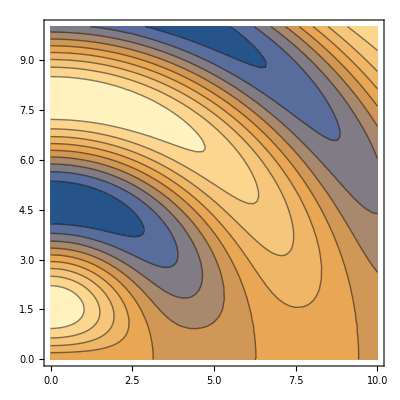

```mathematica
ContourPlot[Cos[ArcTan[x/y]]*Sin[Sqrt[x^2+y^2]],{x,0,10},{y,0,10}]
```

```mathematica
SphericalPlot3D[Evaluate@Table[Sqrt[((1+Cos[θ]^2)/2)^2+Cos[θ]^2]*(2*ϕ/(2*Pi*f)+t)/.{f-> 1},{t,0,0}],{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

```mathematica
Table[hx[t,1,θ,ϕ]/.{f->1,Mchirp->1},{t,0,1,0.2}]
```

{-4 π^(2/3) Cos[θ] Sin[6.28319-2 ϕ],-4 π^(2/3) Cos[θ] Sin[5.02655-2 ϕ],-4 π^(2/3) Cos[θ] Sin[3.76991-2 ϕ],-4 π^(2/3) Cos[θ] Sin[2.51327-2 ϕ],-4 π^(2/3) Cos[θ] Sin[1.25664-2 ϕ],4 π^(2/3) Cos[θ] Sin[0.+2 ϕ]}

```mathematica
Evaluate@Table[r*hx[t,r,θ,ϕ]/.{f->1,Mchirp->1},{t,0,0.2,0.2},{r,1,2}]
```

{{-4 π^(2/3) Cos[θ] Sin[6.28319-2 ϕ],-4 π^(2/3) Cos[θ] Sin[12.5664-2 ϕ]},{-4 π^(2/3) Cos[θ] Sin[5.02655-2 ϕ],-4 π^(2/3) Cos[θ] Sin[11.3097-2 ϕ]}}

```mathematica
SphericalPlot3D[Evaluate@Table[r*hx[t,r,θ,ϕ]/.{f->1,Mchirp->1},{t,0,0},{r,1,1.4,0.2}],{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

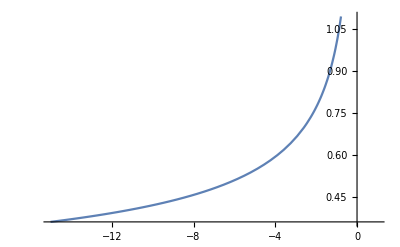

```mathematica
Plot[(-t)^(-3/8),{t,-15,1}]
```

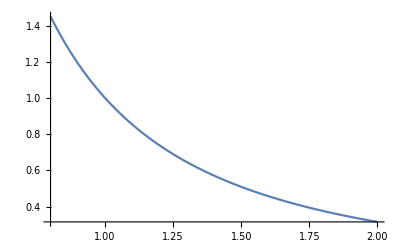

```mathematica
Plot[f^(-5/3),{f,0.8,2}]
```

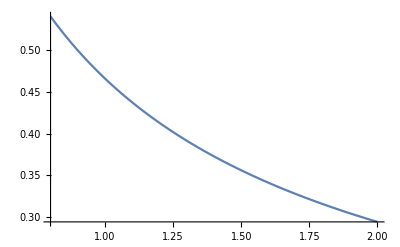

```mathematica
Plot[(Pi*f)^(-2/3),{f,0.8,2}]
```

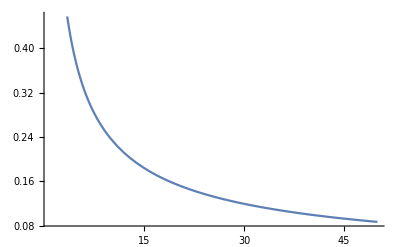

```mathematica
Plot[(M)^(-5/8),{M,1,50}]
```

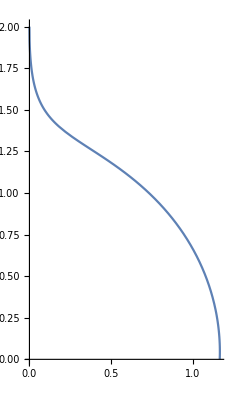

```mathematica
PolarPlot[1+0.2/(((Pi/2-θ)/(Pi/2))^0.5+0.2),{θ,0,Pi/2}]
```